1

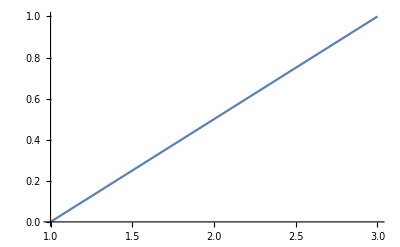

```mathematica
k=1/2;
Integrate[k x-k,{x,1,3}]
Plot[k x-k,{x,1,3}]
```

ⅇ^-x

{x,2,5}

0.128597

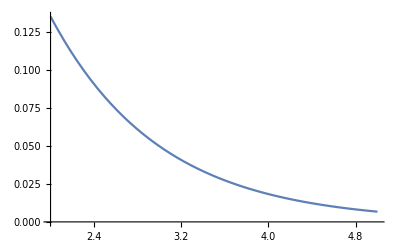

1

```mathematica
g=Exp[-x]
bounds={x,2,5}

A=Integrate[g,bounds];
A//N
k=1/A;
Plot[g,bounds]

f=k g;
Integrate[f,bounds]
```

```mathematica
g=x^2*Exp[-x]
A=Integrate[g,{x,1,4}]
f=g/A
Integrate[f,{x,1,4}](*This should be 1.*)
EV=Integrate[x*f,{x,1,4}]
N[EV,100]
Var=Integrate[(x-EV)^2*f,{x,1,4}]
%//N
stDev=Sqrt[Var]
%//N
Integrate[f,{x,1,3}]//N
```

ⅇ^-x x^2

(-26+5 ⅇ^3)/ⅇ^4

(ⅇ^(4-x) x^2)/(-26+5 ⅇ^3)

1

(2 (-71+8 ⅇ^3))/(-26+5 ⅇ^3)

2.409971392991469514622774891657641918303474624241688575643570734294443390111936445175995785390376695

(3 (420-422 ⅇ^3+23 ⅇ^6))/((26-5 ⅇ^3)^2)

0.66221

(√(3 (420-422 ⅇ^3+23 ⅇ^6)))/(-26+5 ⅇ^3)

0.813763

0.728451

Group Activity

```mathematica
g=Sqrt[49-x^2]
A=Integrate[g,{x,0,7}]
k=1/A
f=k*g
Integrate[f,{x,0,7}]==1
EV=Integrate[x f,{x,0,7}]//N
Var=Integrate[(x-EV)^2 f,{x,0,7}]//N
```

√(49-x^2)

(49 π)/4

4/(49 π)

(4 √(49-x^2))/(49 π)

True

2.97089

3.4238